```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\jitter

```mathematica
data1=Import["multiple.csv"];
data2=Import["miltiple_single.csv"];
```

```mathematica
fontsize=30;
```

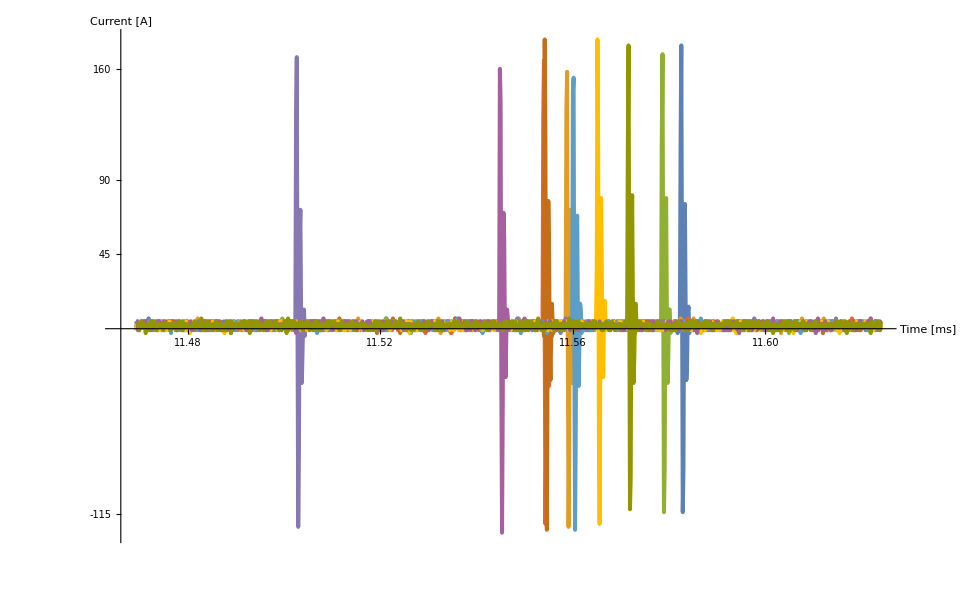

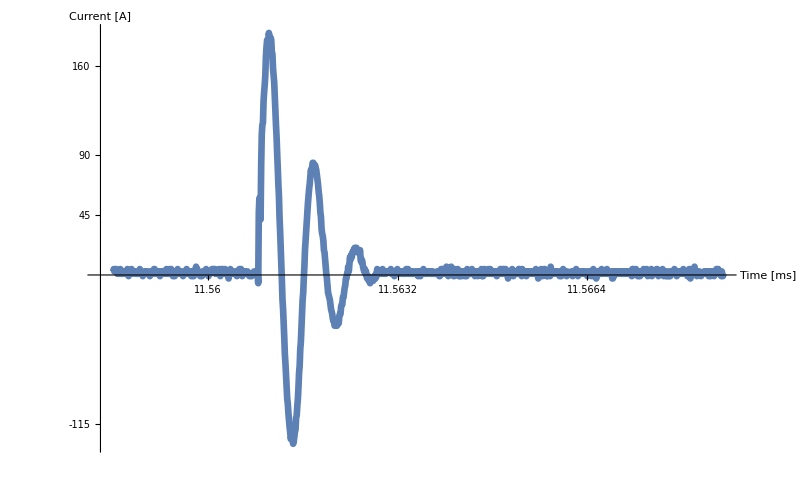

```mathematica
g1=ListLinePlot[
Table[
Thread[{data1⟦All,1⟧,data1⟦All,j⟧}],{j,2,11}],
PlotRange->All,
PlotStyle->{Thickness[0.003]},
TicksStyle->{Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"],Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"]},
AxesStyle->{{Thick,Black},{Thick,Black}},AxesLabel->{Style["Time [ms]",Black,FontFamily->"Helvetica",FontSize->fontsize],Style["Current [A]",Black,FontFamily->"Helvetica",FontSize->fontsize]},
Ticks->
{{{0.01148,11.48,0.06,Directive[Thick]},
{0.01152,11.52,0.06,Directive[Thick]},
{0.01156,11.56,0.06,Directive[Thick]},
{0.01160,"11.60",0.06,Directive[Thick]}}
,{{2,45,0.04},{4,90,0.04},{7,160,0.04},{-5,-115,0.04}}
},
ImageSize->960]
g2=ListLinePlot[Thread[{data2⟦All,1⟧,data2⟦All,2⟧}],PlotRange->All,PlotStyle->{Thickness[0.006]},
TicksStyle->{Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"],Directive[Black,FontSize->fontsize,FontFamily->"Helvetica"]},
AxesStyle->{{Thick,Black},{Thick,Black}},AxesLabel->{Style["Time [ms]",Black,FontFamily->"Helvetica",FontSize->fontsize],Style["Current [A]",Black,FontFamily->"Helvetica",FontSize->fontsize]}
,Ticks->
{{{0.0115568,11.56,0.06,Directive[Thick]},
{0.01156,11.5632,0.06,Directive[Thick]},
{0.0115632,11.5664,0.06,Directive[Thick]}}
,{{2,45,0.04},{4,90,0.04},{7,160,0.04},{-5,-115,0.04}}
}
,ImageSize->960/1.2]
```

```mathematica
color=Lighter[Black,0.3];
Show[{GraphicsColumn[{g1,g2}],
Graphics[{
{Thick,color,Line[{ImageScaled[{0.52,0.68}],ImageScaled[{0.26,0.39}]}]}
,{Thick,color,Line[{ImageScaled[{0.54,0.68}],ImageScaled[{0.43,0.02}]}]}
,{EdgeForm[{Thick,color}],FaceForm[],Rectangle[ImageScaled[{0.52,0.65}],ImageScaled[{0.54,0.72}]]}
,{EdgeForm[{Thick,color}],FaceForm[],Rectangle[ImageScaled[{0.26,0.02}],ImageScaled[{0.43,0.39}]]}
}]}
,ImageSize->960
,PlotRange->All]
```

-Graphics-